# Two-level system

Giuseppe D’Auria

Physics Department, University of Trieste

```mathematica
ClearAll["Global`*"]
```

Define the Pauli matrices.

```mathematica
Subscript[σ, x]=PauliMatrix[1];
Subscript[σ, z]=PauliMatrix[3];
```

Define the Hamiltonian.

```mathematica
H=-Δ*Subscript[σ, z]-γ*Subscript[σ, x];
```

Define the initial state |L>:

```mathematica
initialState={0,1};
```

Define the time evolution operator

```mathematica
U[t_]=MatrixExp[-I H t/ħ];
```

Calculate the state at time t

```mathematica
ψt=U[t].initialState;
```

Calculate the tunneling probability to state |R>

```mathematica
tunnelingProbability=Abs[ψt[[1]]]^2
```

Abs[-(ⅇ^(-(ⅈ t √(γ^2+Δ^2))/ħ) γ)/(2 √(γ^2+Δ^2))+(ⅇ^((ⅈ t √(γ^2+Δ^2))/ħ) γ)/(2 √(γ^2+Δ^2))]^2

```mathematica
simplifiedTunnelingProbabilityTrig=ComplexExpand[tunnelingProbability,TargetFunctions->{Re,Im}]
```

(γ^2 Sin[(t √(γ^2+Δ^2))/ħ]^2)/(γ^2+Δ^2)

Write the solution in terms of ω and γ:

```mathematica
solutions=Solve[ω ^2==Δ^2+γ^2,Δ]
simplifiedTunnelingProbabilityTrig/.solutions[[1]]//FullSimplify
```

{{Δ→-√(-γ^2+ω^2)},{Δ→√(-γ^2+ω^2)}}

(γ^2 Sin[(t ω)/ħ]^2)/ω^2

Define the tunneling probability in terms of ω and γ

```mathematica
NewtunnelingProbability[ω_,γ_,t_]=(γ^2 Sin[(ω t)/ħ]^2)/ω^2;
```

Differentiate the tunneling probability with respect to t

```mathematica
NewtunnelingProbability[ω,γ,t]
```

(γ^2 Sin[(t ω)/ħ]^2)/ω^2

```mathematica
dPdt[ω_,γ_,t_]=D[NewtunnelingProbability[ω,γ,t],t]//FullSimplify
```

(γ^2 Sin[(2 t ω)/ħ])/(ħ ω)

Set the derivative to zero and solve for t

```mathematica
DerivSol=Solve[dPdt[ω,γ,t]==0,t]//FullSimplify
```

{{t→ConditionalExpression[(ħ π C[1])/ω,C[1]∈ℤ]},{t→ConditionalExpression[(ħ (π+2 π C[1]))/(2 ω),C[1]∈ℤ]}}

Find the corresponding maximum value of the tunneling probability

```mathematica
maxTunnelingProbability=NewtunnelingProbability[ω,γ,t]/.DerivSol[[2]]
```

ConditionalExpression[(γ^2 Sin[1/2 (π+2 π C[1])]^2)/ω^2,C[1]∈ℤ]

Find the corresponding maximum value of the tunneling probability

```mathematica
maxTunnelingProbability=NewtunnelingProbability[ω,γ,t]/.DerivSol[[2]]
```

ConditionalExpression[(γ^2 Sin[1/2 (π+2 π C[1])]^2)/ω^2,C[1]∈ℤ]

Print the result

```mathematica
maxTunnelingProbability//FullSimplify
```

ConditionalExpression[γ^2/ω^2,C[1]∈ℤ]

Write t^* in a better way

```mathematica
DerivSol[[2]]
```

{t→ConditionalExpression[(ħ (π+2 π C[1]))/(2 ω),C[1]∈ℤ]}

```mathematica
ComplexExpand[DerivSol[[2]],TargetFunctions->{Re,Im}]
```

{t→ConditionalExpression[(ħ π)/(2 ω)+(ħ π C[1])/ω,C[1]∈ℤ]}

Now define t^* with the value just found

```mathematica
SuperStar[t]=ComplexExpand[DerivSol[[2]],TargetFunctions->{Re,Im}]
```

{t→ConditionalExpression[(ħ π)/(2 ω)+(ħ π C[1])/ω,C[1]∈ℤ]}

Check of consistency if t^*is the point of maximum

```mathematica
NewtunnelingProbability[ω,γ,t]/. SuperStar[t]//FullSimplify
```

ConditionalExpression[γ^2/ω^2,C[1]∈ℤ]

Plot the probability of tunneling

```mathematica
PlottunnelingProbability[ω_,γ_,t_]=(γ^2 Sin[(ω t)/ħ]^2)/ω^2;
```

Specify values for ω and γ

```mathematica
ω=Sqrt[1.25]; (*Replace with your specific value for ω*)
γ=0.5; (*Replace with your specific value for γ*)
ħ =1;
PlottunnelingProbability[ω,γ,t];
```

Plot the tunneling probability as a function of time t

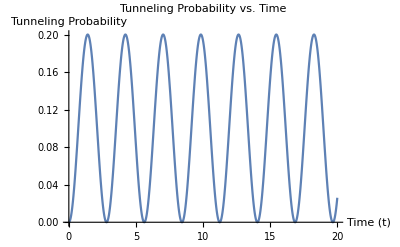

```mathematica
Plot[PlottunnelingProbability[ω,γ,t],{t,0,20},AxesLabel->{"Time (t)","Tunneling Probability"},PlotLabel->"Tunneling Probability vs. Time"]
```

```mathematica
solutions=Solve[ω ^2==Δ^2+γ^2,Δ]
```

{{Δ→-1.},{Δ→1.}}

```mathematica
simplifiedTunnelingProbabilityTrig
```

(0.25 Sin[t √(0.25+Δ^2)]^2)/(0.25+Δ^2)

```mathematica
DeltatunnelingProbability[Δ_,γ_,t_]:=(γ^2 Sin[(t √(γ^2+Δ^2))/ħ]^2)/(γ^2+Δ^2)
```

```mathematica
Δ=1.0; (*Replace with your specific value for Δ*)
γ=0.5; (*Replace with your specific value for γ*)
ħ =1;
```

```mathematica
Plot[DeltatunnelingProbability[Δ, γ, t], {t, 0, 20}, AxesLabel -> {"Time (t)", "Tunneling Probability"}, PlotLabel -> "Tunneling Probability vs. Time"]
```

-Graphics-

```mathematica
Δ^2 + γ^2
```

1.25